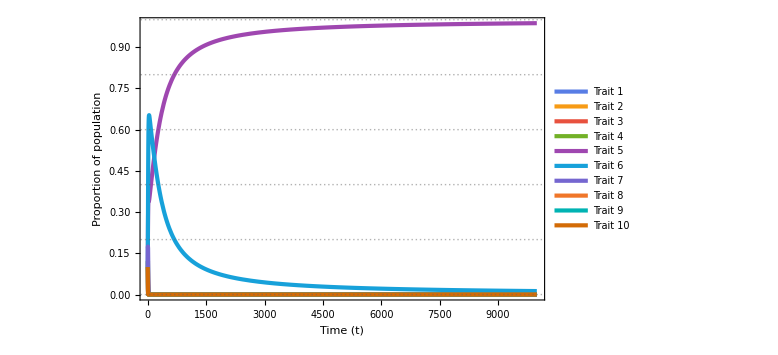

```mathematica
n = 10;
T1 = Table[i,{i,n}];
b;

t = Table[Subscript[r, i],{i,n}];
males= Table[Subscript[m, i],{i,n}];
females = Table[Subscript[f, i],{i,n}];
denom = Total[males];

dm = Table[0,{i,n}];
df = Table[0,{i,n}];

For[i = 1, i < n+1, i++,
dm[[i]] =(b/denom)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[(x+ y)/2 == i],{x,1,n},{y,1,n}]
];

For[i = 1, i <n +1, i++,
dm[[i]] = dm[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[Floor[(x+ y)/2] == i && (x+y)/2 ≠ Floor[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i <n +1, i++,
dm[[i]] = dm[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[Ceiling[(x+ y)/2] == i && (x+y)/2 ≠ Ceiling[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i < n+1, i++,
df[[i]] =(b/denom)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[(x+ y)/2 == i],{x,1,n},{y,1,n}]
];

For[i = 1, i <n +1, i++,
df[[i]] = df[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[Floor[(x+ y)/2] == i && (x+y)/2 ≠ Floor[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i <n +1, i++,
df[[i]] = df[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[Ceiling[(x+ y)/2] == i && (x+y)/2 ≠ Ceiling[(x+ y)/2]],{x,1,n},{y,1,n}]
]

all = FullSimplify[Total[dm]];
denom2 = Total[females /. {Subscript[f, p_]:> Subscript[y, p]}];

f[p_] := Subscript[y, p] *denom
h[q_] := If[q < n, Subscript[x, q]*denom, (1-Sum[Subscript[x, i],{i,1,n-1}])*denom]
g[z_] := If[z <n, Subscript[q, z]*denom2 , (1-Sum[Subscript[q, i],{i,1,n-1}])*denom2];
e[z_] := If[z <n, Subscript[q, z], (1-Sum[Subscript[q, i],{i,1,n-1}])];

t1[z_] :=Subscript[y, z][s];
t2[z_] := Subscript[x, z][s];

dm2 = Table[0,{i,n}];
df2 = Table[0,{i,n}];

For[ i = 1,i < n+1,i++,
dm2[[i]] = FullSimplify[(dm[[i]])/denom -(males[[i]]/denom^2)*all  /. {Subscript[f, q_] :>f[q], Subscript[m, p_] :> h[p] }];
]

For[ i = 1,i < n+1,i++,
df2[[i]] = FullSimplify[(df[[i]])/denom -(females[[i]]/denom^2)*all/. {Subscript[f, q_] :>f[q], Subscript[m, p_] :> h[p] }];
]


mfinal = Table[0,{i,n-1}];
ffinal = Table[0,{i,n}];
vartab = List[];
ic = List[];


For[ i = 1,i < n,i++,
mfinal[[i]] = Subscript[x, i]'[s] == FullSimplify[dm2[[i]] /. {Subscript[x, z_] :>t2[z],Subscript[y, z_] :>t1[z]}]
];

For[ i = 1,i<n,i++,
AppendTo[vartab,Subscript[x, i]
]];

For[i = 1,i<n+1,i++,
AppendTo[vartab,Subscript[y, i]]];

For[ i = 1,i<n,i++,
AppendTo[ic,Subscript[x, i][0] == (1/n)]
];

For[i = 1,i<n+1,i++,
AppendTo[ic,Subscript[y, i][0] == 1]
];

For[i = 1,i<n+1,i++,
ffinal[[i]] = Subscript[y, i]'[s] == FullSimplify[df2[[i]] /. {Subscript[x, z_] :>t2[z],Subscript[y, z_] :>t1[z]}]];

mfinal;
ffinal;
vartab;
ic;

eqlist = Join[mfinal,ffinal,ic];

traits = Table[Subscript[r, i],{i,1,n}];
For[i = 1,i<n+1,i++,
Subscript[r, i] = i/n
]

b = 1;
tmax = 10^4;

sol:= NDSolve[eqlist,vartab,{s,0,tmax}];

plots = {};

For[ i = 1,i<n+1,i++,
If[i ≠ n,AppendTo[plots, {(Subscript[x, i][s] + Subscript[y, i][s])/(1 + Sum[Subscript[y, j][s],{j,1,n}])  }],AppendTo[plots,{(1-Sum[Subscript[x, j][s],{j,1,n-1}] + Subscript[y, i][s])/(1 + Sum[Subscript[y, k][s],{k,1,n}])  }]]
]

leglabels = Table[ StringJoin["Trait ",ToString[i]],{i,1,n}];

a = Plot[Evaluate[plots/.sol],{s,0,tmax},PlotRange -> All,PlotLegends -> LineLegend[leglabels,LabelStyle -> {"Grey"}],PlotTheme->"Business",ImageSize -> Large,FrameLabel -> {Style["Time (t)",13,FontColor -> "Black"],Style["Proportion of population",13,FontColor -> "Black"]},FrameTicksStyle->Black]
```